## 0.-Definiciones previas (copia todas las que necesites de ficheros de clase y si quieres definir alguna nueva)

Ejes coordenados

```mathematica
(*ejes*)ejes:=Graphics3D[{Red,Dashed,Arrow[{{-1,0,0},{2.5,0,0}}],Blue,Arrow[{{0,-1,0},{0,2.5,0}}],Yellow,Arrow[{{0,0,-1},{0,0,2.5}}]}]
B[n_,i_,t_]:=Binomial[n,i]*tt^i*(1-tt)^(n-i)/.tt->t (*Polinomios de Bernstein*)
B[n_,i_][t_]:=Binomial[n,i]*tt^i*(1-tt)^(n-i)/.tt->t
CurvaBezier[poligono_][t_]:=Sum[B[Length[poligono]-1,i,t]*poligono[[i+1]],{i,0,Length[poligono]-1}]//ExpandAll (*Curva de Bezier*)

M[n_][valort_,puntos_] :=Table[Table[B[n, i, valort[[j + 1]]],{i, 0,n}],  {j, 0, Length[puntos]-1}](*Matriz de Ajuste*)

(*n es el grado de la curva de Bézier (n+1 puntos de control)*)
A[n_][valort_,puntos_]:=Inverse[Transpose[M[n][valort,puntos]].M[n][valort,puntos]].Transpose[M[n][valort,puntos]]
approx[puntos_,valort_,n_]:=A[n][valort,puntos].puntos(*//Chop*) (*Cálculo de los puntos de control*)


Dibuja[poligono_]:=Show[Graphics[Line[poligono]],Graphics[Table[{Red,PointSize[Large],Point[poligono[[i+1]]]},{i,0,Length[poligono]-1}]],
ParametricPlot[CurvaBezier[poligono][t],{t,0,1},PlotStyle->Blue]]
```

```mathematica
supBezier[red_][u_,v_]:=Sum[B[Length[red]-1,i,u]*B[Length[red[[1]]]-1,j,v]*red[[i+1,j+1]],{i,0,Length[red]-1},{j,0,Length[red[[1]]]-1}]//Simplify//ExpandAll
```

```mathematica
supBezier2[red_][u_,v_,a_,b_,c_,d_]:=Sum[B[Length[red]-1,i][(u-a)/(b-a)]*B[Length[red[[1]]]-1,j][(v-c)/(d-c)]*red[[i+1,j+1]],{i,0,Length[red]-1},{j,0,Length[red[[1]]]-1}]//Simplify//ExpandAll (*nuestro rectángulo de parametrización es [0,π/2]×[0,2]*)
```

```mathematica
(* Matriz del cambio de base {polinomios de Berstein}  a la de potencias  {1,t,t^2,t^3,...,t^n} *)
MC[n_]:=Table[CoefficientList[B[n,i,t],t],{i,0,n}]
```

```mathematica
coef[poli_,n_,t_]:=If[Length[CoefficientList[poli,t]]-1>n,"No se puede, grado base Bernstein demasiado bajo" ,Join[CoefficientList[poli,t],Table[0,{i,1,n+1-Length[CoefficientList[poli,t]]}]].Inverse[MC[n]]]
```

```mathematica
denoSup[sup_][u_,v_]:=PolynomialLCM[Denominator[sup[u,v]][[1]],Denominator[sup[u,v]][[2]],Denominator[sup[u,v]][[3]]]//Simplify;
numSup[sup_][u_,v_]:=denoSup[sup][u,v]*sup[u,v]//Simplify
```

```mathematica
CurvaBezierRacional[poligono_,pesos_][t_]:=
Sum[B[Length[poligono]-1,i,t]*poligono[[i+1]]*pesos[[i+1]],{i,0,Length[poligono]-1}]/
Sum[B[Length[poligono]-1,i,t]*pesos[[i+1]],{i,0,Length[poligono]-1}]//Simplify
```

```mathematica
supBezRac[red_,pesos_][u_,v_]:=Sum[pesos[[i+1,j+1]]*red[[i+1,j+1]]B[Length[red]-1,i][u]B[Length[red[[1]]]-1,j][v],{i,0,Length[red]-1},{j,0,Length[red[[1]]]-1}]/Sum[pesos[[i+1,j+1]]B[Length[red]-1,i][u]B[Length[red[[1]]]-1,j][v],{i,0,Length[red]-1},{j,0,Length[red[[1]]]-1}]//Simplify
```

```mathematica
mCoef[sup_][u_,v_,m_,n_]:=Table[Coefficient[Coefficient[sup[u,v],u,i],v,j],{i,0,m},{j,0,n}]
mUsBer[n_]:=Inverse[Table[CoefficientList[B[n,i][t],t],{i,0,n}]]
```

```mathematica
pesosSup[sup_,m_,n_]:=If[Length[CoefficientList[denoSup[sup][u,v],u]]-1>m ||Length[CoefficientList[denoSup[sup][u,v],v]]-1>n ,"No se puede, grado base Bernstein demasiado bajo" ,Transpose[mUsBer[m]].Table[Table[Sum[mCoef[denoSup[sup]][u,v,m,n][[i+1,j+1]]mUsBer[n][[j+1,k+1]],{j,0,n}],{k,0,n}],{i,0,m}]]//Simplify
```

```mathematica
(*Puntos de control de la superfície racional de grados m y n *)puntContRac[sup_,m_,n_]:=If[Max[Table[Length[CoefficientList[numSup[sup][u,v][[i]],u]],{i,1,3}]]-1>m ||Max[Table[Length[CoefficientList[numSup[sup][u,v][[i]],v]],{i,1,3}]]-1>n ,"No se puede, grado base Bernstein demasiado bajo" ,Transpose[mUsBer[m]].Table[Table[Sum[mCoef[numSup[sup]][u,v,m,n][[i+1,j+1]]mUsBer[n][[j+1,k+1]],{j,0,n}],{k,0,n}],{i,0,m}]]/pesosSup[sup,m,n]//Simplify
```

```mathematica
red[n_]:=Map[ToExpression[StringJoin["P",#]]&,
Apply[StringJoin,Map[ToString,Table[{i,j},{i,0,n},{j,0,n}],{-1}],{2}],{-1}]
```

```mathematica
condArmo[sup_][u_,v_]:=Flatten[CoefficientList[CoefficientList[D[sup[u,v],{u,2}]+D[sup[u,v],{v,2}]//Simplify,u],v]]
```

# Gráficas

```mathematica
c19 = {46722,34638,62084,132930,207088,273201,317067,334073,339091,336055,324535,302135,279431,256731,233107,210700,190089,169635,150732,133141,117116,101956,88686,76681,65325,54863,45830,37354,29997,23823,18384,14758,12078,9970,8435,6981,5927,5125,4507,4049,3508,3134,2782,2496,2269,2045};
c20 = {23674,17589,29465,61370,99009,131994,152524,161997,165797,164198,159452,151221,140831,131117,118890,107848,98412,88335,79673,71530,62856,55356,48373,40664,35245,29511,24043,19668,15922,12496,9430,7515,6081,4971,4279,3476,2930,2544,2166,1965,1747,1481,1312,1115,1024,951};
```

```mathematica
tiempos = Subdivide[Length[c19]];
```

```mathematica
puntos19 = Table[{i,c19[[i]]},{i,Length[c19]}];
puntos20 = Table[{i,c20[[i]]},{i,Length[c19]}];
```

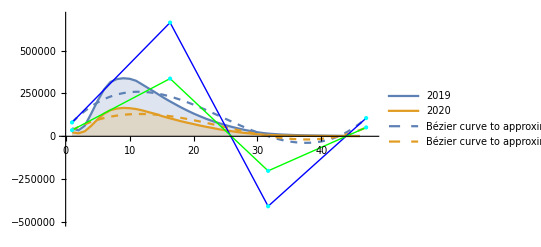

```mathematica
n=3;
puntosControl19=N[approx[puntos19,tiempos,n]]; (*Puntos de control*)
puntosControl19Dibujo=Table[{PointSize->Large,Cyan,Point[puntosControl19[[i]]]},{i,Length[puntosControl19]}]; 
bezier19[t_]:=CurvaBezier[puntosControl19][t]

puntosControl20=N[approx[puntos20,tiempos,n]]; (*Puntos de control*)
puntosControl20Dibujo=Table[{PointSize->Large,Cyan,Point[puntosControl20[[i]]]},{i,Length[puntosControl20]}]; 
bezier20[t_]:=CurvaBezier[puntosControl20][t] 
Show[
ListPlot[{c19,c20},Filling->Axis,Joined->True,PlotRange->{{0,48},{-500000.3779058023,700000.9485048489}},PlotLegends->{"2019","2020"}],
ParametricPlot[{bezier19[t],bezier20[t]},{t,0,1},PlotStyle->Dashed,PlotLegends->{"Bézier curve to approximate 2019","Bézier curve to approximate 2020"}],
Graphics[{Blue,Line[puntosControl19],PointSize[Medium],puntosControl19Dibujo,Green,Line[puntosControl20],PointSize[Medium],puntosControl20Dibujo}]

]
```

```mathematica
puntosControl19
```

{{1.,80905.},{16.3333,664433.},{31.6667,-408684.},{47.,106333.}}

```mathematica
p1 = Show[
ListPlot[{c19,c20},Filling->Axis,Joined->True,PlotRange->{{0,48},{-500000.3779058023,700000.9485048489}},PlotLegends->{"2019","2020"}],
ParametricPlot[{bezier19[t],bezier20[t]},{t,0,1},PlotStyle->Dashed,PlotLegends->{"Bézier curve to approximate 2019","Bézier curve to approximate 2020"}],
Graphics[{Blue,Line[puntosControl19],PointSize[Medium],puntosControl19Dibujo,Green,Line[puntosControl20],PointSize[Medium],puntosControl20Dibujo}]

]
```

```mathematica
SetDirectory["D:\\Desktop\\Estudios\\UNIVERSIDAD\\Investmat\\TFM\\codigos_final_2\\graphics_new"]
```

D:\Desktop\Estudios\UNIVERSIDAD\Investmat\TFM\codigos_final_2\graphics_new

```mathematica
Export["bezier_curvas_tiempos_ejemplo.png",p1]
```

bezier_curvas_tiempos_ejemplo.png